## Brian — PS 9 — 2025-02-21 — Solution

## EIWL3 Sections 23, 24, and 25

## Exercises from EIWL3 Section 23

```mathematica
(* 23.1 *) N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

```mathematica
(* 23.2 *) RandomReal[1,10]
```

{0.124788,0.0504512,0.23143,0.453413,0.024918,0.480212,0.1928,0.445133,0.205133,0.680719}

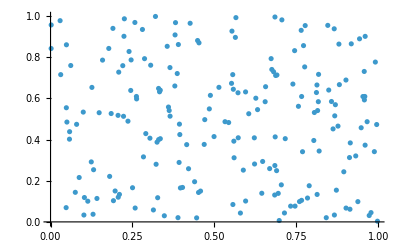

```mathematica
(* 23.3 *) ListPlot[RandomReal[1,{200,2}]]
```

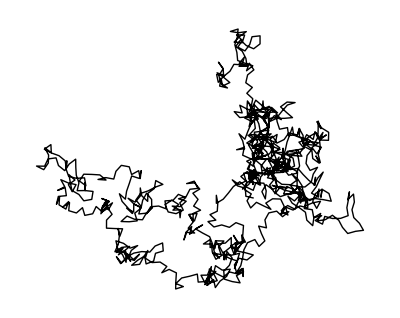

```mathematica
(* 23.4 *) Graphics[Line[AnglePath[RandomReal[2Pi,1000]]]]
```

```mathematica
(* 23.5 *) Table[Mod[n^2,10],{n,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

```mathematica
(* 23.6 *) Table[Mod[n^n,10],{n,100}]
```

{1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0,1,4,7,6,5,6,3,6,9,0,1,6,3,6,5,6,7,4,9,0}

```mathematica
(* 23.7 *) Round[Table[Pi^i,{i,10}]]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

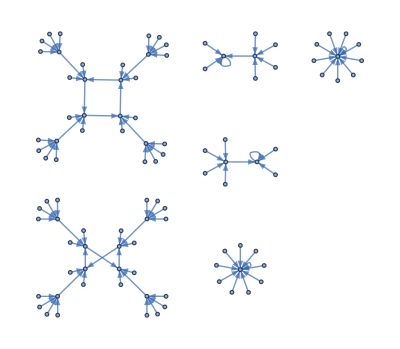

```mathematica
(* 23.8 *) Graph[Table[n->Mod[n^2,100],{n,0,99}]]
```

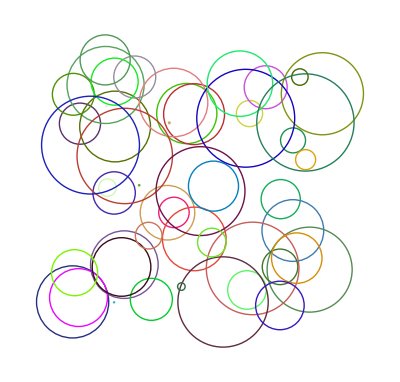

```mathematica
(* 23.9 *) Graphics[Table[
Style[Circle[{RandomReal[10],RandomReal[10]},RandomReal[2]],RandomColor[]],
50]]
(* This is an expression that is just complicated enough that I decided to use indenting to help me write it out correctly. *)
```

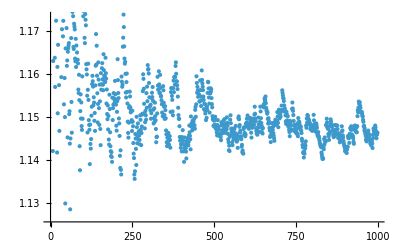

```mathematica
(* 23.10 *) ListPlot[Table[Prime[n]/(n Log[n]),{n,2,1000}]]
```

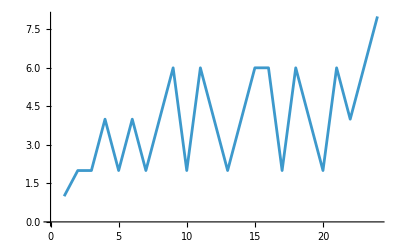

```mathematica
(* 23.11 *) ListLinePlot[Table[Prime[n]-Prime[n-1],{n,2,25}]]
(* I am not sure how we were supposed to know that the 25th prime was *)
(* the last one less than 100. I just did trial and error to figure that out. *)
```

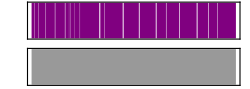

```mathematica
(* 23.12 *) Sound[Table[SoundNote[0, RandomReal[0.5]],20]]
```

## Exercises from EIWL3 Section 24

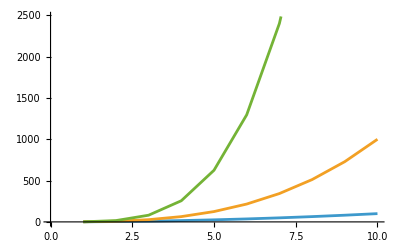

```mathematica
(* 24.1 *) ListLinePlot[{Range[10]^2,Range[10]^3,Range[10]^4}]
```

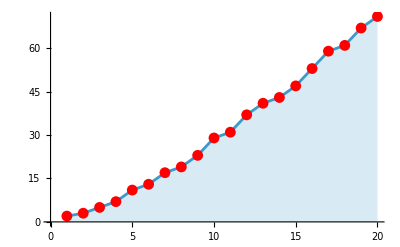

```mathematica
(* 24.2 *) ListLinePlot[Table[Prime[i],{i,20}],Filling->Axis,Mesh->All,MeshStyle->Red]
```

```mathematica
(* 24.3 *) ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[20, "Miles"]]],PlotRange->All]
```

-Graphics3D-

```mathematica
(* 24.4 *) ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],Quantity[100, "Miles"]]]]
```

-Graphics-

```mathematica
(* 24.5 *) ListPlot3D[Table[Mod[i,j],{i,100},{j,100}]]
```

-Graphics3D-

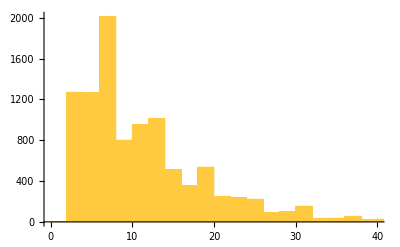

```mathematica
(* 24.6 *) Histogram[Table[Prime[j+1]-Prime[j],{j,9999}]]
```

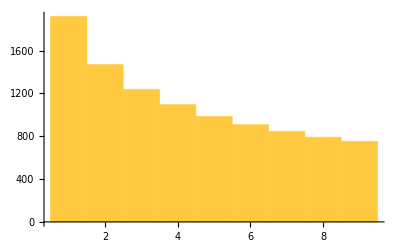

```mathematica
(* 24.7 *) Histogram[Table[First[IntegerDigits[j^2]],{j,10000}]]
```

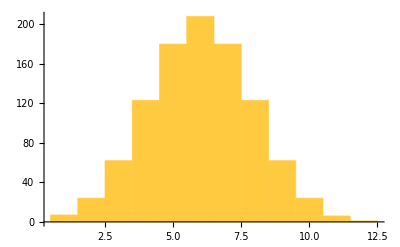

```mathematica
(* 24.8 *) Histogram[Table[StringLength[RomanNumeral[i]],{i,1000}]]
```

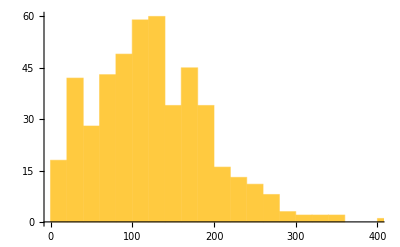

```mathematica
(* 24.9 *) Histogram[StringLength[TextSentences[WikipediaData["Computers"]]]]
```

```mathematica
(* 24.10 *) Table[Table[Total[RandomReal[100.0,n]],2],{n,1,5}]
```

{{93.3351,11.3423},{137.963,56.3913},{146.049,187.884},{232.187,156.564},{305.846,320.849}}

```mathematica
(* 24.11 *) ListPlot3D[ImageData[Binarize[Graphics[Style[Text["W"],200]]]]]
```

-Graphics3D-

## Exercises from EIWL3 Section 25

```mathematica
(* 25.1 *)
```